Defining the true PDF f_X(x), Kernel g(x,y), and the efficiency ϵ(x)

```mathematica
f[x_]:= 1/3 PDF[CauchyDistribution[12,2],x]+2/3 PDF[CauchyDistribution[19,2],x];
g[x_,y_]:=PDF[NormalDistribution[-2(Log[Abs[x]+1])^(1/3),2Exp[-Abs[x]/30]],y-x];
ϵ[x_]:=(1-Exp[-Abs[x]/80])^(1/4);
```

The sequence over the plotting domain of x and y for plotting xys, the values of the true PDF f_x(x) for plotting, fxs. The binned true pdf histxs.

```mathematica
xys =Table[N[x/100],{x,0,3000}];
fxs = N[f[xys]];
histxs = N[Table[∫_(i-1)^i f[x]ⅆx,{i,1,30}]];
```

Point-by-point calculation of the measured PDF f_Y(y) across each histogram bin separately, fysd[[i]]. The mean for each to get the expected weight of each bin, histys. The bins combined into the values to be plotted of f_y(y), fys.

```mathematica
fysd = Table[Null,{x,1,30}];
fysd[[1]] = NIntegrate[ExpandAll[f[x]ϵ[x]g[x,N[Table[x/100,{x,0,100}]]]],{x,-∞,∞}];
fysd[[2]] = NIntegrate[ExpandAll[f[x]ϵ[x]g[x,N[Table[x/100,{x,100,200}]]]],{x,-∞,∞}];
fysd[[3]] = NIntegrate[ExpandAll[f[x]ϵ[x]g[x,N[Table[x/100,{x,200,300}]]]],{x,-∞,∞}];
fysd[[4]] = NIntegrate[ExpandAll[f[x]ϵ[x]g[x,N[Table[x/100,{x,300,400}]]]],{x,-∞,∞}];
fysd[[5]] = NIntegrate[ExpandAll[f[x]ϵ[x]g[x,N[Table[x/100,{x,400,500}]]]],{x,-∞,∞}];
fysd[[6]] = NIntegrate[ExpandAll[f[x]ϵ[x]g[x,N[Table[x/100,{x,500,600}]]]],{x,-∞,∞}];
fysd[[7]] = NIntegrate[ExpandAll[f[x]ϵ[x]g[x,N[Table[x/100,{x,600,700}]]]],{x,-∞,∞}];
fysd[[8]] = NIntegrate[ExpandAll[f[x]ϵ[x]g[x,N[Table[x/100,{x,700,800}]]]],{x,-∞,∞}];
fysd[[9]] = NIntegrate[ExpandAll[f[x]ϵ[x]g[x,N[Table[x/100,{x,800,900}]]]],{x,-∞,∞}];
fysd[[10]] = NIntegrate[ExpandAll[f[x]ϵ[x]g[x,N[Table[x/100,{x,900,1000}]]]],{x,-∞,∞}];
fysd[[11]] = NIntegrate[ExpandAll[f[x]ϵ[x]g[x,N[Table[x/100,{x,1000,1100}]]]],{x,-∞,∞}];
fysd[[12]] = NIntegrate[ExpandAll[f[x]ϵ[x]g[x,N[Table[x/100,{x,1100,1200}]]]],{x,-∞,∞}];
fysd[[13]] = NIntegrate[ExpandAll[f[x]ϵ[x]g[x,N[Table[x/100,{x,1200,1300}]]]],{x,-∞,∞}];
fysd[[14]] = NIntegrate[ExpandAll[f[x]ϵ[x]g[x,N[Table[x/100,{x,1300,1400}]]]],{x,-∞,∞}];
fysd[[15]] = NIntegrate[ExpandAll[f[x]ϵ[x]g[x,N[Table[x/100,{x,1400,1500}]]]],{x,-∞,∞}];
fysd[[16]] = NIntegrate[ExpandAll[f[x]ϵ[x]g[x,N[Table[x/100,{x,1500,1600}]]]],{x,-∞,∞}];
fysd[[17]] = NIntegrate[ExpandAll[f[x]ϵ[x]g[x,N[Table[x/100,{x,1600,1700}]]]],{x,-∞,∞}];
fysd[[18]] = NIntegrate[ExpandAll[f[x]ϵ[x]g[x,N[Table[x/100,{x,1700,1800}]]]],{x,-∞,∞}];
fysd[[19]] = NIntegrate[ExpandAll[f[x]ϵ[x]g[x,N[Table[x/100,{x,1800,1900}]]]],{x,-∞,∞}];
fysd[[20]] = NIntegrate[ExpandAll[f[x]ϵ[x]g[x,N[Table[x/100,{x,1900,2000}]]]],{x,-∞,∞}];
fysd[[21]] = NIntegrate[ExpandAll[f[x]ϵ[x]g[x,N[Table[x/100,{x,2000,2100}]]]],{x,-∞,∞}];
fysd[[22]] = NIntegrate[ExpandAll[f[x]ϵ[x]g[x,N[Table[x/100,{x,2100,2200}]]]],{x,-∞,∞}];
fysd[[23]] = NIntegrate[ExpandAll[f[x]ϵ[x]g[x,N[Table[x/100,{x,2200,2300}]]]],{x,-∞,∞}];
fysd[[24]] = NIntegrate[ExpandAll[f[x]ϵ[x]g[x,N[Table[x/100,{x,2300,2400}]]]],{x,-∞,∞},AccuracyGoal->100,MaxRecursion->500, MinRecursion-> 400];
fysd[[25]] = NIntegrate[ExpandAll[f[x]g[x,N[Table[x/100,{x,2400,2500}]]]],{x,-∞,∞}];
fysd[[26]] = NIntegrate[ExpandAll[f[x]g[x,N[Table[x/100,{x,2500,2600}]]]],{x,-∞,∞},AccuracyGoal->100,MaxRecursion->800, MinRecursion-> 600];
fysd[[27]] = NIntegrate[ExpandAll[f[x]g[x,N[Table[x/100,{x,2600,2700}]]]],{x,-∞,∞}];
fysd[[28]] = NIntegrate[ExpandAll[f[x]g[x,N[Table[x/100,{x,2700,2800}]]]],{x,-∞,∞}];
fysd[[29]] = NIntegrate[ExpandAll[f[x]g[x,N[Table[x/100,{x,2800,2900}]]]],{x,-∞,∞}];
fysd[[30]] = NIntegrate[ExpandAll[f[x]g[x,N[Table[x/100,{x,2900,3000}]]]],{x,-∞,∞}];
histys =Table[Mean[fysd[[i]]],{i,1,30}];
seq =Table[x,{x,2,101}];
fys = Flatten[Join[{fysd[[1]]},Table[fysd[[i]][[seq]],{i,2,30}]]];
```

Plotting fxs, fys, histxs, and histys.

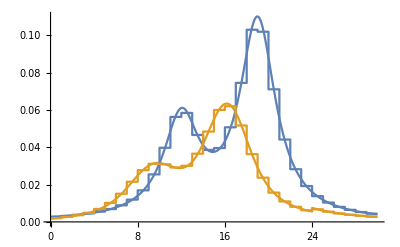

```mathematica
Show[ListLinePlot[{Transpose[{xys,fxs}],Transpose[{xys,fys}]}],
ListStepPlot[{Transpose[{Table[x,{x,0,29}],histxs}],Transpose[{Table[x,{x,0,29}],histys}]}]]
```

Defining columns of table to be used for plotting histxs and histxy in R.

```mathematica
hbinl = Join[Table[x,{x,0,29}],Table[x,{x,0,29}]];
hbinh = Join[Table[x,{x,1,30}],Table[x,{x,1,30}]];
hcountl = Join[{0},histxs[[Table[x,{x,1,29}]]],
{0},histys[[Table[x,{x,1,29}]]]];
hcount = Join[histxs,histys];
treat = Join[Table["not folded",{x,1,30}],Table["folded",{x,1,30}]];
```

Saving plotting data to their appropriate files.

```mathematica
SetDirectory[NotebookDirectory[]];
Export["fyEstimate.csv",
Transpose[{PrependTo[xys,Y],PrependTo[fys,Density]}]];
Export["histExpected.csv",
Transpose[{PrependTo[hbinl,binLow],PrependTo[hbinh,binHigh],
PrependTo[hcountl,CountsL],PrependTo[hcount,Counts],
PrependTo[treat,Treatment]}]];
```